```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 834 Kb

{Utilities`CleanSlate`,VariationalMethods`,DocumentationSearch`,ResourceLocator`,System`,Global`}

```mathematica
Clear[q]
q = { x[t],y[t], θ[t],ϕ[t] } 
q[[1]]
q[[2]]
q[[3]]
q[[4]]
```

{x[t],y[t],θ[t],ϕ[t]}

x[t]

y[t]

θ[t]

ϕ[t]

```mathematica
D[q, t]
D[q[[1]], t]
D[q[[2]], t]
```

{x'[t],y'[t],θ'[t],ϕ'[t]}

x'[t]

y'[t]

```mathematica
Clear[r1]
r1 = { x[t] , y[t] }
```

{x[t],y[t]}

```mathematica
D[r1, t]
```

{x'[t],y'[t]}

```mathematica
D[r1, t] . D[r1, t]
```

x'[t]^2+y'[t]^2

```mathematica
Clear[r2] 
r2 = { x[t] + b Cos[θ[t]] , y[t] + b Sin[θ[t]] }
```

{b Cos[θ[t]]+x[t],b Sin[θ[t]]+y[t]}

```mathematica
D[r2, t]
```

{x'[t]-b Sin[θ[t]] θ'[t],y'[t]+b Cos[θ[t]] θ'[t]}

```mathematica
D[r2, t] . D[r2, t]
```

(y'[t]+b Cos[θ[t]] θ'[t])^2+(x'[t]-b Sin[θ[t]] θ'[t])^2

```mathematica
Clear[T] 
T = 1/2 M ( D[r1, t] . D[r1, t] ) +1/2(1/2 M R^2 θ'[t]^2) + 1/2 m (D[r2, t] . D[r2, t]) + 1/2(1/2 m r^2) ϕ'[t]^2
```

1/2 M (x'[t]^2+y'[t]^2)+1/4 M R^2 θ'[t]^2+1/2 m ((y'[t]+b Cos[θ[t]] θ'[t])^2+(x'[t]-b Sin[θ[t]] θ'[t])^2)+1/4 m r^2 ϕ'[t]^2

```mathematica
Clear[V]
V = 0
```

0

```mathematica
Clear[ℒ]
ℒ = T - V
```

1/2 M (x'[t]^2+y'[t]^2)+1/4 M R^2 θ'[t]^2+1/2 m ((y'[t]+b Cos[θ[t]] θ'[t])^2+(x'[t]-b Sin[θ[t]] θ'[t])^2)+1/4 m r^2 ϕ'[t]^2

```mathematica
D[ D[ ℒ , D[q[[1]], t] ] ,t]- D[ ℒ , q[[1]] ] 
D[ D[ ℒ , D[q[[2]], t] ] ,t]- D[ ℒ , q[[2]] ] 
D[ D[ ℒ , D[q[[3]], t] ] ,t]- D[ ℒ , q[[3]] ] // Expand // Simplify 
D[ D[ ℒ , D[q[[4]], t] ] ,t]- D[ ℒ , q[[4]] ] 

Table[
D[ D[ ℒ , D[q[[i]], t] ] ,t]- D[ ℒ , q[[i]] ],
{i,1,4} ] // Expand // Simplify // TableForm
```

M x''[t]+m (-b Cos[θ[t]] θ'[t]^2+x''[t]-b Sin[θ[t]] θ''[t])

M y''[t]+m (-b Sin[θ[t]] θ'[t]^2+y''[t]+b Cos[θ[t]] θ''[t])

-b m Sin[θ[t]] x''[t]+b m Cos[θ[t]] y''[t]+1/2 (2 b^2 m+M R^2) θ''[t]

1/2 m r^2 ϕ''[t]

-b m Cos[θ[t]] θ'[t]^2+(m+M) x''[t]-b m Sin[θ[t]] θ''[t]
-b m Sin[θ[t]] θ'[t]^2+(m+M) y''[t]+b m Cos[θ[t]] θ''[t]
-b m Sin[θ[t]] x''[t]+b m Cos[θ[t]] y''[t]+1/2 (2 b^2 m+M R^2) θ''[t]
1/2 m r^2 ϕ''[t]

```mathematica
Clear[eqs]
eqs = EulerEquations[ ℒ, q, t ] ;
eqs // TableForm
```

b m Cos[θ[t]] θ'[t]^2-(m+M) x''[t]+b m Sin[θ[t]] θ''[t]==0
b m Sin[θ[t]] θ'[t]^2-(m+M) y''[t]-b m Cos[θ[t]] θ''[t]==0
b m Sin[θ[t]] x''[t]-b m Cos[θ[t]] y''[t]-1/2 (2 b^2 m+M R^2) θ''[t]==0
-1/2 m r^2 ϕ''[t]==0

```mathematica
FirstIntegrals[ ℒ , q, t ] // TableForm
```

FirstIntegral[x]→-(m+M) x'[t]+b m Sin[θ[t]] θ'[t]
FirstIntegral[y]→-(m+M) y'[t]-b m Cos[θ[t]] θ'[t]
FirstIntegral[ϕ]→-1/2 m r^2 ϕ'[t]
FirstIntegral[t]→1/4 (2 (m+M) x'[t]^2+2 (m+M) y'[t]^2-4 b m Sin[θ[t]] x'[t] θ'[t]+4 b m Cos[θ[t]] y'[t] θ'[t]+2 b^2 m θ'[t]^2+M R^2 θ'[t]^2+m r^2 ϕ'[t]^2)

```mathematica
Clear[m,M,r,R,b]
M= 10 ;
m = 2;
R = 5 ;
r = 1 ;
b = 2 ;
```

```mathematica
Clear[ics]
ics = { 
x[0] == 1,
x'[0] == -2 ,
y[0] == 3,
y'[0] == -4 ,
θ[0] == 5,
θ'[0] == - 6,
ϕ[0] == 7 ,
ϕ'[0] == -8 
} ;
ics // TableForm
```

x[0]==1
x'[0]==-2
y[0]==3
y'[0]==-4
θ[0]==5
θ'[0]==-6
ϕ[0]==7
ϕ'[0]==-8

```mathematica
Clear[solution]
solution = 
NDSolve[ Union[eqs,ics] , q, { t, 0, 10 } ]
```

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t],ϕ[t]→InterpolatingFunction[…][t]}}

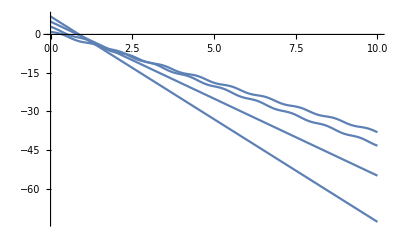

```mathematica
Plot[ q /. solution, { t, 0, 10 } ]
```

```mathematica
(* Clear[problem2002]
Manipulate[
problem2002 = Module[ {q,ℒ,eqs,ics,solution} ,
Clear[q];
q = { x[t],y[t], θ[t],ϕ[t] } ;
Clear[r1];
r1 = { x[t] , y[t] } ;
       Clear[r2]; 
r2 = { x[t] + b Cos[θ[t]] , y[t] + b Sin[θ[t]] } ;
       Clear[T] ;
T = 1/2 M ( ∂_t r1 . ∂_t r1 ) +1/2(1/2 M R^2 θ'[t]^2) + 1/2 m (∂_t r2 . ∂_t r2) + 1/2(1/2 m r^2) ϕ'[t]^2 ;
       Clear[V];
V = 0  ;
       Clear[ℒ];
ℒ = T - V  ;
       Clear[eqs];
eqs = EulerEquations[ ℒ, q, t ] ;
Clear[m,M,r,R,b];
M= 10 ;
(* m = 2; *) 
R = 5 ;
r = 1 ;
b = 2 ;
 Clear[ics];
ics = { 
x[0] == x0,
x'[0] == vx0 ,
y[0] == y0,
y'[0] == vy0 ,
θ[0] == θ0,
θ'[0] == vθ0,
ϕ[0] == ϕ0 ,
ϕ'[0] == vϕ0 
} ;
Clear[solution];
solution = 
NDSolve[ Union[eqs,ics] , q, { t, 0, 10 } ] ;
Plot[ q /. solution, { t, 0, 10 } ]],
{m, 0.1, 1 } , 
{x0,-3,3},{vx0,-3,3},
{y0,-3,3},{vy0,-3,3},
{ θ0,-3,3}, {vθ0,-3,3},
{ϕ0,-3,3}, {vϕ0,-3,3} ] 
*)
```